# Autovalores de U en un rectangulo de 10 x 5

Caminata cuantica en tiempo continuo. El kernel principal esta en el Mac; el calculo se ejecuta en nodo1 mediante Mazinger. Este ejemplo carga solo Rectangle.wl y CTQW.wl, sin instalar paclets ni guardar archivos en el cluster.

## Modelo

GenerateRectangleBasis[9, 4] incluye las coordenadas 0..9 y 0..4: 10 x 5 = 50 sitios. Con gamma = 1, el paquete define H = A - D, donde A es la matriz de adyacencia y D la matriz diagonal de grados. Para tiempo t = 1 usamos U = Exp[-I H].

## Calculo en nodo1

```mathematica
resultadoRectangulo = RemoteEvaluate["ssh://robot", RemoteEvaluate["ssh://nodo1", Module[{ruta, base, h, u, vals}, ruta = "/home/saul/QW/JA_libs/QuantumWalks"; BeginPackage["QuantumWalks`"]; EndPackage[]; Get[FileNameJoin[{ruta, "Billiards", "Rectangle.wl"}]]; Get[FileNameJoin[{ruta, "CTQW.wl"}]]; base = QuantumWalks`Billiards`GenerateRectangleBasis[9, 4]; h = QuantumWalks`CTQW`CTQWHamiltonian[base, 1.0]; u = MatrixExp[-I h]; vals = Eigenvalues[u]; <|"Nodo" -> $MachineName, "Dimension" -> Dimensions[u], "Autovalores" -> vals, "ErrorMaximoModulo" -> Max[Abs[Abs[vals] - 1]]|>]]]
```

<|Nodo→nodo1,Dimension→{50,50},Autovalores→{-0.989992+0.14112 ⅈ,-0.971249-0.238065 ⅈ,-0.416147+0.909297 ⅈ,-0.839557-0.543271 ⅈ,-0.154234-0.988034 ⅈ,0.579336+0.815089 ⅈ,0.972056+0.23475 ⅈ,0.35639+0.934337 ⅈ,0.87254+0.488543 ⅈ,0.283662-0.958924 ⅈ,-0.989992+0.14112 ⅈ,-0.955079-0.296352 ⅈ,-0.653644-0.756802 ⅈ,-0.094215-0.995552 ⅈ,-0.191937+0.981407 ⅈ,-0.866045+0.499965 ⅈ,-0.888633-0.45862 ⅈ,0.887063+0.461649 ⅈ,0.927934+0.372746 ⅈ,-0.888633-0.45862 ⅈ,0.927934+0.372746 ⅈ,-0.653644-0.756802 ⅈ,-0.59366+0.804716 ⅈ,-0.866045+0.499965 ⅈ,0.995213+0.0977307 ⅈ,0.18771+0.982224 ⅈ,-0.725093+0.688651 ⅈ,-0.653644-0.756802 ⅈ,0.327668+0.944793 ⅈ,-0.92953+0.368747 ⅈ,-0.415334-0.909669 ⅈ,0.18771+0.982224 ⅈ,-0.191937+0.981407 ⅈ,0.99889-0.0470999 ⅈ,1.+1.03113×10^-15 ⅈ,0.283662-0.958924 ⅈ,-0.914735-0.404053 ⅈ,0.678976+0.734161 ⅈ,-0.26666-0.963791 ⅈ,0.500069-0.865985 ⅈ,-0.910762+0.412933 ⅈ,0.541054-0.840988 ⅈ,0.786823-0.617178 ⅈ,-0.724477-0.689299 ⅈ,0.722122+0.691766 ⅈ,0.090818+0.995868 ⅈ,0.99889-0.0470999 ⅈ,-0.999423-0.0339713 ⅈ,-0.653644-0.756802 ⅈ,0.88253-0.470256 ⅈ},ErrorMaximoModulo→2.88658×10^-15|>

El resultado contiene los autovalores y una comprobacion de que U es unitario: cada autovalor debe tener modulo cercano a 1.

## Resumen

```mathematica
{resultadoRectangulo["Nodo"], resultadoRectangulo["Dimension"], Length[resultadoRectangulo["Autovalores"]], resultadoRectangulo["ErrorMaximoModulo"]}
```

{nodo1,{50,50},50,2.88658×10^-15}

Resultado esperado: {"nodo1", {50, 50}, 50, un numero cercano a 10^-15}.

## Autovalores

```mathematica
resultadoRectangulo["Autovalores"]
```

{-0.989992+0.14112 ⅈ,-0.971249-0.238065 ⅈ,-0.416147+0.909297 ⅈ,-0.839557-0.543271 ⅈ,-0.154234-0.988034 ⅈ,0.579336+0.815089 ⅈ,0.972056+0.23475 ⅈ,0.35639+0.934337 ⅈ,0.87254+0.488543 ⅈ,0.283662-0.958924 ⅈ,-0.989992+0.14112 ⅈ,-0.955079-0.296352 ⅈ,-0.653644-0.756802 ⅈ,-0.094215-0.995552 ⅈ,-0.191937+0.981407 ⅈ,-0.866045+0.499965 ⅈ,-0.888633-0.45862 ⅈ,0.887063+0.461649 ⅈ,0.927934+0.372746 ⅈ,-0.888633-0.45862 ⅈ,0.927934+0.372746 ⅈ,-0.653644-0.756802 ⅈ,-0.59366+0.804716 ⅈ,-0.866045+0.499965 ⅈ,0.995213+0.0977307 ⅈ,0.18771+0.982224 ⅈ,-0.725093+0.688651 ⅈ,-0.653644-0.756802 ⅈ,0.327668+0.944793 ⅈ,-0.92953+0.368747 ⅈ,-0.415334-0.909669 ⅈ,0.18771+0.982224 ⅈ,-0.191937+0.981407 ⅈ,0.99889-0.0470999 ⅈ,1.+1.03113×10^-15 ⅈ,0.283662-0.958924 ⅈ,-0.914735-0.404053 ⅈ,0.678976+0.734161 ⅈ,-0.26666-0.963791 ⅈ,0.500069-0.865985 ⅈ,-0.910762+0.412933 ⅈ,0.541054-0.840988 ⅈ,0.786823-0.617178 ⅈ,-0.724477-0.689299 ⅈ,0.722122+0.691766 ⅈ,0.090818+0.995868 ⅈ,0.99889-0.0470999 ⅈ,-0.999423-0.0339713 ⅈ,-0.653644-0.756802 ⅈ,0.88253-0.470256 ⅈ}

## Grafica en el plano complejo

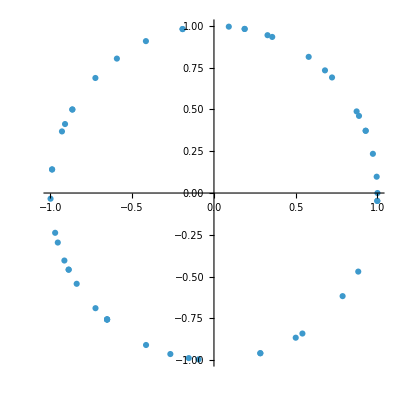

```mathematica
ComplexListPlot[resultadoRectangulo["Autovalores"], PlotRange -> All, AspectRatio -> 1]
```

Los puntos deben quedar sobre el circulo unitario. La grafica se dibuja en tu Mac con los 50 autovalores recibidos desde nodo1.